```mathematica
spherePoint[dim_]:=Table[RandomVariate[NormalDistribution[]],dim]//Normalize;
```

```mathematica
randomPointInBall[dim_]:=spherePoint[dim]*RandomReal[]^(1/dim);
```

```mathematica
zeroInsideSimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords},
lastVertexNewCoords=-Last[vertices].Inverse[m];
AllTrue[lastVertexNewCoords,#>=0&]&&Total[lastVertexNewCoords]<=1
];
```

```mathematica
feasibilifySimplex[vertices_]:=Module[{m=#-Last[vertices]&/@Most[vertices],lastVertexNewCoords,multipliers},
lastVertexNewCoords=-Last[vertices].Inverse[m];
multipliers=Append[If[#>=0,1,-1]&/@lastVertexNewCoords,If[Total[lastVertexNewCoords]<=1,1,-1]];
vertices*multipliers
];
```

```mathematica
generateSimplexWithZeroInside[dim_]:=feasibilifySimplex[Table[spherePoint[dim],dim+1]];
```

```mathematica
exportSimplexInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim],openAppend=OpenAppend[filename],delta},
(*delta=-SignedRegionDistance[Simplex[vertices],Table[0,dim]]//N;*)
Export[openAppend,"# first line is delta, then "<>ToString[dim+1]<>" lines with vertices\n","Text"];
Export[openAppend,ToString["delta"]<>"\n","Text"];
Export[openAppend,vertices,"CSV"];
];
```

```mathematica
exportSimplexPlusBallInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim],openAppend=OpenAppend[filename],delta,radius=RandomReal[]},
(*delta=N[-SignedRegionDistance[Simplex[vertices],Table[0,dim]]];*)
Export[openAppend,"# A = simplex + ball, B = unit ball, t = 1, x = 0\n","Text"];
Export[openAppend,"# first line is the radius of the ball, second line is delta, then "<>ToString[dim+1]<>" lines with vertices of the simplex\n","Text"];
Export[openAppend,ToString[NumberForm[radius,16]]<>"\n","Text"];
Export[openAppend,ToString["delta"]<>"\n","Text"];
Export[openAppend,vertices*(1-radius),"CSV"];
];
```

```mathematica
exportDegenerateSimplexInBallExample[dim_,filename_]:=Module[
{vertices=generateSimplexWithZeroInside[dim-1],openAppend=OpenAppend[filename]},
Export[openAppend,"# "<>ToString[dim]<>" lines with vertices\n","Text"];
Export[openAppend,Table[PrependTo[vertices[[i]],0],{i,dim}],"CSV"];
];
```

```mathematica
exportPolyhedronInBallExample[dim_,filename_]:=Module[
{basedVertices=generateSimplexWithZeroInside[dim],restVertices=Table[randomPointInBall[dim],{dim+1}],openAppend=OpenAppend[filename]},
Export[openAppend,"# the first line is minimal distance from non-based vertices to the sphere, then "<>ToString[2*(dim+1)]<>" lines with vertices\n","Text"];
Export[openAppend,ToString[NumberForm[Min[(1-Norm[#])&/@restVertices],16]]<>"\n","Text"];
Export[openAppend,Join[basedVertices,restVertices],"CSV"];
];
```

```mathematica
(*Do[
exportSimplexPlusBallInBallExample[100,NotebookDirectory[]<>"tests/100d/simplex-plus-ball-in-ball/"<>ToString[n]],{n,100}]*)
exportSimplexPlusBallInBallExample[20,NotebookDirectory[]<>"tests/20d/simplex-plus-ball-in-ball/90"]
```

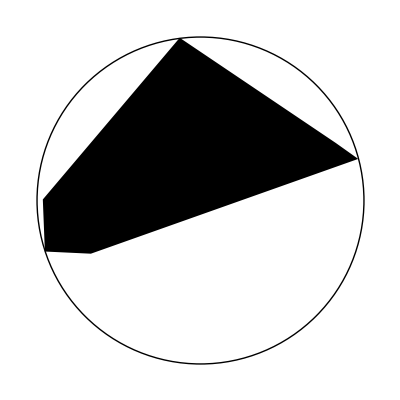

```mathematica
vertices=Join[generateSimplexWithZeroInside[2],Table[randomPointInBall[2],2*2]];
Graphics[{ConvexHullRegion[vertices],Circle[]}]
```

```mathematica
Norm[{-0.3124363569624589,-0.5755042157701786,-0.41665662845131246}]-1
```

-0.22384